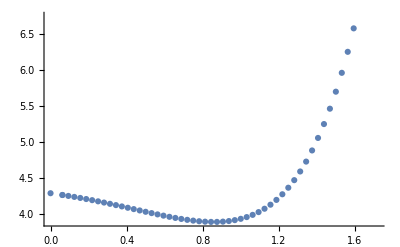

```mathematica
c={{0,4.289559},{0.062500,4.264998},{0.062500,4.264998},{0.093750,4.251975},{0.125000,4.238299},{0.156250,4.223933},{0.187500,4.208871},{0.218750,4.193132},{0.250000,4.176751},{0.281250,4.159781},{0.312500,4.142287},{0.343750,4.124348},{0.375000,4.106052},{0.406250,4.087502},{0.437500,4.068810},{0.468750,4.050102},{0.500000,4.031517},{0.531250,4.013207},{0.562500,3.995339},{0.593750,3.978095},{0.625000,3.961677},{0.656250,3.946302},{0.687500,3.932210},{0.718750,3.919663},{0.750000,3.908946},{0.781250,3.900373},{0.812500,3.894287},{0.843750,3.891062},{0.875000,3.891111},{0.906250,3.894883},{0.937500,3.902875},{0.968750,3.915630},{1.000000,3.933746},{1.031250,3.957880},{1.062500,3.988755},{1.093750,4.027167},{1.125000,4.073993},{1.156250,4.130194},{1.187500,4.196823},{1.218750,4.275028},{1.250000,4.366043},{1.281250,4.471173},{1.312500,4.591749},{1.343750,4.729037},{1.375000,4.884112},{1.406250,5.057765},{1.437500,5.250736},{1.468750,5.464322},{1.500000,5.700691},{1.531250,5.962839},{1.562500,6.254618},{1.593750,6.580712},{1.625000,6.945955},{1.656250,7.352624},{1.687500,7.792152},{1.718750,8.224919}};
ListPlot[c]
```

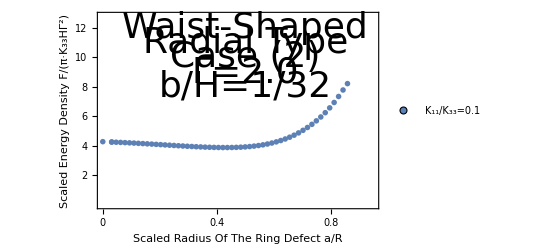

```mathematica
bb=c*Table[{0.5,1},{i,0,55}];
ListPlot[{bb},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{2,4,6,8,10,12},None},{{0,0.2, 0.4, 0.6, 0.8,1.0},None}}, PlotRange->{{0,0.95},{0,12.8}},FrameLabel->{{"Scaled Energy Density F/(π·K_33HΓ^2)", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=0.1","K_11/K_33=2.0","K_11/K_33=3.0","K_11/K_33=4.0"},LegendMarkers->{{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12}}],{Left, Top}],Epilog->{Text[Style["Waist-Shaped",Directive[Black,36]],{0.5,12}],Text[Style["Radial Type",Directive[Black,36]],{0.5,11}],Text[Style["Case (2)",Directive[Black,36]],{0.5,10}],Text[Style["Γ=2.0",Directive[Black,36]],{0.5,9}],Text[Style["b/H=1/32",Directive[Black,36]],{0.5,8}]}]
```